```mathematica
ClearAll["Global'*"]
G[r1_,r2_]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G2[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G3[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
```

```mathematica
g1[r1_,r2_]={r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))};
g2[r1_,r2_]={r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))};
```

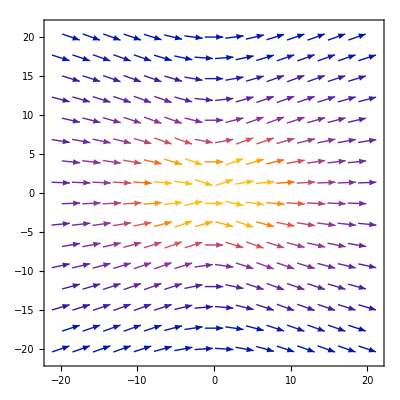

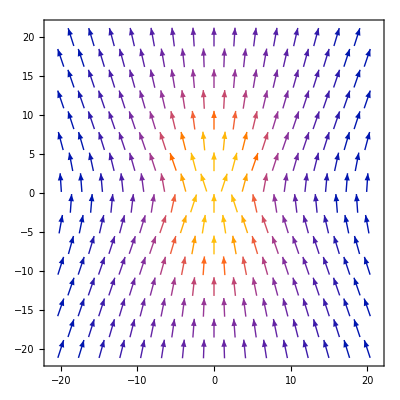

```mathematica
VectorPlot[g1[x,y],{x,-20,20},{y,-20,20}]
VectorPlot[g2[x,y],{x,-20,20},{y,-20,20}]
```

```mathematica
y0:={100,100}
```

```mathematica
y0hat:=y0/Norm[y0];
```

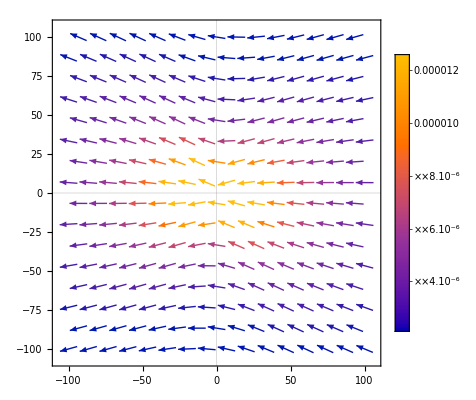

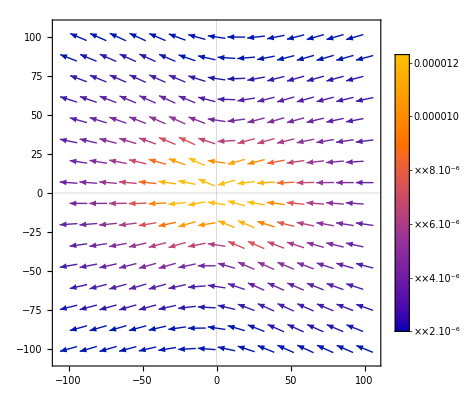

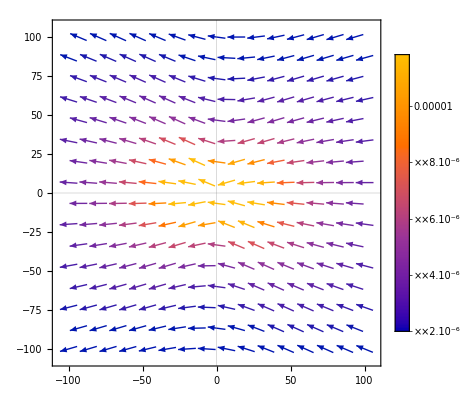

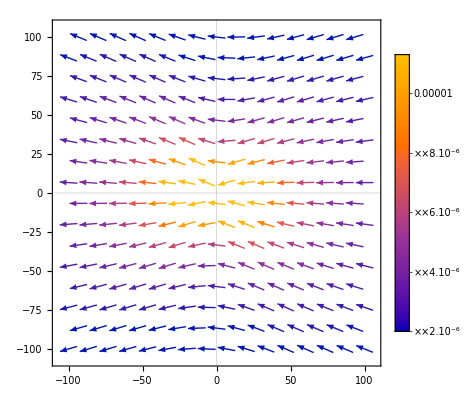

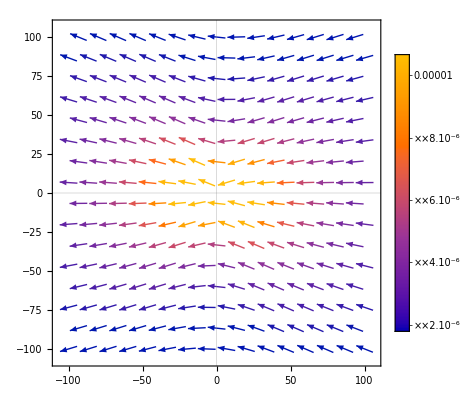

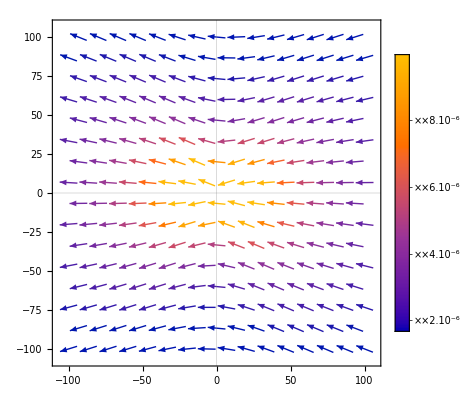

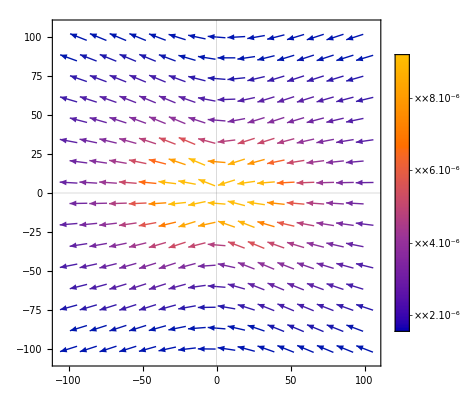

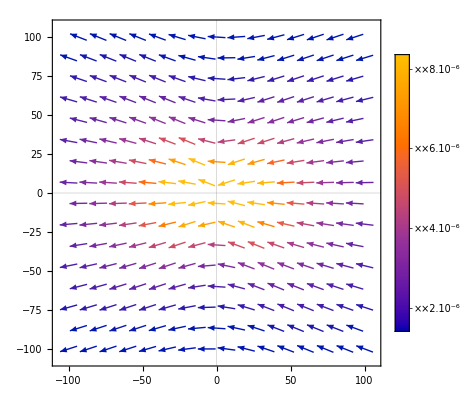

$Aborted

```mathematica
For[i = 1,i≤128,i++,
theta=2Pi i/128;
epsilon:=1/Norm[y0];
  x1[t_]:={2,0}+RotationMatrix[theta].{Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}],0};
x2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx1[t_]:=RotationMatrix[theta].{Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}],0};
dx2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
x11[t_?NumericQ]:={2,0}+RotationMatrix[theta].{Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}],0};
x21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx11[t_?NumericQ]:=RotationMatrix[theta].{Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}],0};
dx21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
(*Print[Plot[{x1[t][[1]],x2[t][[2]]},{t,0,1},PlotLegends->LineLegend[{"x_{12}","x_{21}"},LegendFunction->Frame],PlotTheme->"Detailed"]];
Print[Plot[{dx1[t][[2]],dx2[t][[1]]},{t,0,1},PlotTheme->"Detailed"]];*)
a=0.1;
mu=1;
Ginv[{r1_,r2_},a_]={{(2 (r1^2+2 r2^2))/(3 a √(r1^2+r2^2)),-(2 r1 r2)/(3 a √(r1^2+r2^2))},{-(2 r1 r2)/(3 a √(r1^2+r2^2)),(2 (2 r1^2+r2^2))/(3 a √(r1^2+r2^2))}};
K[{r1_,r2_},a_]={{(9 a^2 (-9 a^2+8 r1^2+2 r2^2))/(4 (-8 (r1^2+r2^2)^2+9 a^2 (5 r1^2+6 r1 r2+5 r2^2))),(81 a^4+54 a^2 r1 r2)/(4 (-8 (r1^2+r2^2)^2+9 a^2 (5 r1^2+6 r1 r2+5 r2^2)))},{(81 a^4+54 a^2 r1 r2)/(4 (-8 (r1^2+r2^2)^2+9 a^2 (5 r1^2+6 r1 r2+5 r2^2))),(9 a^2 (-9 a^2+2 r1^2+8 r2^2))/(4 (-8 (r1^2+r2^2)^2+9 a^2 (5 r1^2+6 r1 r2+5 r2^2)))}};
f1[t_]=K[x1[t]-x2[t],a].(Ginv[x1[t]-x2[t],a].dx1[t]-(Ginv[x1[t]-x2[t],a].Ginv[x1[t]-x2[t],a]).dx2[t]);
f2[t_]=K[x1[t]-x2[t],a].(Ginv[x1[t]-x2[t],a].dx2[t]-(Ginv[x1[t]-x2[t],a].Ginv[x1[t]-x2[t],a]).dx1[t]);
(*Print[Plot[f1[t],{t,0,1},PlotTheme->"Detailed",PlotRange->All]];
Print[Plot[f2[t],{t,0,1},PlotTheme->"Detailed",PlotRange->All]];*)
diffforces = ParametricNDSolveValue[{c'[t] == G2[c[t] - x11[t]].f1[t] + G2[c[t] - x21[t]].f2[t], c[0] == {b1,b2}}, c[1]-c[0],{t, 0, 1}, {b1,b2}, Method -> "StiffnessSwitching"];
intf=NIntegrate[{f1[t]+f2[t]},{t,0,1}][[1]];
diffforcesapprox[p_?NumericQ,q_?NumericQ] =(G2[{p,q}/((p^2+q^2)^(1/2))]/((p^2+q^2)^(1/2))).intf;
(*Print[FullSimplify[(G2[{p,q}/((p^2+q^2)^(1/2))]/((p^2+q^2)^(1/2))).intf]]*);
plot=VectorPlot[diffforcesapprox[p,q],{p,-100,100},{q,-100,100},PlotTheme->"Scientific",PlotLegends->Automatic,ColorFunction->"TemperatureMap"];
Export[StringJoin["vectorplot",IntegerString[i,10,2],".png"],plot];
Print[plot];
]
```

```mathematica
Directory[]
```

C:\Users\Michael\Documents